(2 π)/7

{0,(2 π)/7,(4 π)/7,(6 π)/7,(8 π)/7,(10 π)/7,(12 π)/7,2 π}

{{0,0},{(2 π)/7,√((2 π)/7)},{(4 π)/7,2 √(π/7)},{(6 π)/7,√((6 π)/7)},{(8 π)/7,2 √((2 π)/7)},{(10 π)/7,√((10 π)/7)},{(12 π)/7,2 √((3 π)/7)},{2 π,√(2 π)}}

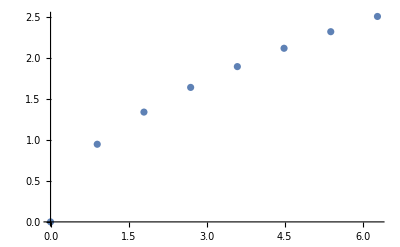

```mathematica
f[x_]:=Sqrt[x]
Np=8;Ni=Np-1;dx=2Pi/Ni
xv=Table[i,{i,0,2Pi,dx}]
fxv=Table[{xv[[i]],f[xv[[i]]]},{i,1,Np}]
ListPlot[fxv]
```

```mathematica
{{0,0},{(2 π)/3,(√3)/2},{(4 π)/3,-(√3)/2},{2 π,0}}
```

{{0,0},{(2 π)/3,(√3)/2},{(4 π)/3,-(√3)/2},{2 π,0}}